```mathematica
ep=0.08;β=0.8;γ=0.5;xmin=-50;xmax=50;maxtime=100; dd1=0.5;dd2=0.001;δ=7.5;
eqn=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
(*d2=1.5;d1=1;
ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*no block*)*)
ρ1=1;slope=0.2;
ρ[x_]=Which[x<0,0,x<ρ1/slope,x * slope,x<2ρ1/slope, 2ρ1-x*slope, True,0];
(*ρ[x_]=Which[x<0,0,x<ρ1/slope,x * slope,True,ρ1];*)
(*eqn1=FindRoot[(1-ρ1^2/2)v-v^3/3-(v+β)/γ,{v,-1}];*)
eqn1=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v1,w1}={v,(v+β)/γ}/.eqn1;
If[1-v0^2<Min[ep γ,1/γ],"(v0,w0) is locally exponentially stable"]
If[1-(v1/Sqrt[1-ρ1^2/2])^2<Min[ep γ /(1-ρ1^2/2)^2,Sqrt[1-ρ1^2/2]/γ],"(v1,w1) is locally exponentially stable"]
```

(v0,w0) is locally exponentially stable

(v1,w1) is locally exponentially stable

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

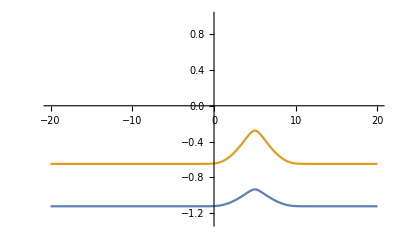

```mathematica
(*Step 1: Starting from the equilibrium, lead to an ok initial guess*)
{V1,W1}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==Which[x<0,v0,True,v1], 
u[t, xmin] == v0, 
u[t, xmax] == v1, w[0, x] ==Which[x<0,w0,True,w1], w[t, xmin] == w0,w[t, xmax] == w1}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
{V2,W2}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==V1[maxtime,x], 
u[t, xmin] == v0, 
u[t, xmax] == v1, w[0, x] ==W1[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w1}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{V2[maxtime,x],W2[maxtime,x]},{x,-20,20},PlotRange->{-1.3,1}]
```

```mathematica
(*Step 3: First approximation to autonomus solution, uses previous iteration*)
{V3,W3}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == dd2  D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] ==  V2[maxtime,x] +Which[Abs[x-45] <=1, 5, True, 0], 
u[t, xmin] == v0, 
u[t, xmax] == v1, w[0, x] == W2[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w1}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

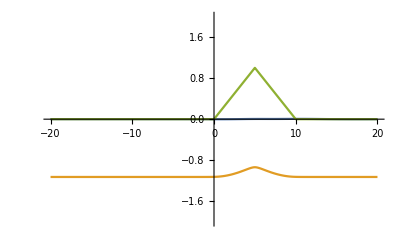

-Graphics3D-

```mathematica
Plot[{V3[maxtime,x]-V2[maxtime,x],V2[maxtime,x],ρ[x]},{x,-20,20},PlotRange->{-2,2}]
Plot3D[V3[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
Animate[Plot[{V3[t,x]-V2[maxtime,x],W3[t,x]-W2[maxtime,x]},{x,-50,50},PlotRange->{{-60,60},{-2,2}}],{t,0,100},AnimationRunning->False,AnimationRepetitions->1]
```

```mathematica
Solve[v(1-ρ1^2/2)-v^3/3-w1==0,v]
```

{{v→-0.976781},{v→-0.662446},{v→1.63923}}

```mathematica
maxtime=300;
{V0,W0}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - (2/3)(1-ρ[x]^2/2)^(3/2), 
u[0, x] ==Which[x<0,v0,True,1.6392267987597744], 
u[t, xmin] == v0, 
u[t, xmax] ==1.6392267987597744}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

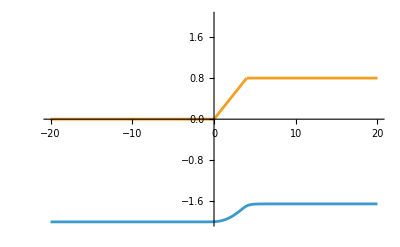

-Graphics3D-

```mathematica
Plot[{V0[maxtime,x],ρ[x]},{x,-20,20},PlotRange->{-2,2}]
Plot3D[V0[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
Animate[Plot[{V0[t,x],W0[t,x]},{x,-50,50},PlotRange->{{-60,60},{-2,2}}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
```